```mathematica
file=FileNameJoin[{NotebookDirectory[],"run1","position_all.txt"}];
```

```mathematica
maxima=Import[file, {"Data",All,3}];
```

```mathematica
mean=Mean[maxima];
ScientificForm[N[mean]]
```

2.07423×10^1

```mathematica
stdDev=StandardDeviation[maxima];
ScientificForm[N[stdDev]]
```

1.33343×10^1

```mathematica
ScientificForm[N[stdDev/mean]]
```

6.42856×10^-1

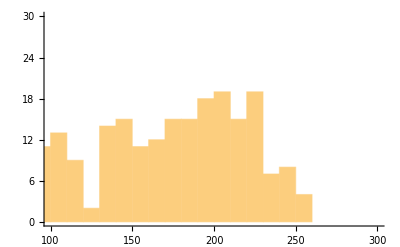

```mathematica
Histogram[maxima,{10},PlotRange->{{100, 300},{0, 30}}]
```

```mathematica
x=Import[file, {"Data",All,1}];
y=Import[file, {"Data",All,2}];
points=Table[{x[[i]],-y[[i]]},{i,1,Length[x]}];
```

```mathematica
VoronoiMesh[points]
```

-Graphics-